```mathematica
Clear["Global`*"];

d = 9;
n=6d;

g[a_]:= (2a +d-2) ((a+d-3)!)/(((d-2)!)(a!));

f = 1/((1-x^(2l+ d-2))^(g[l]));
e = PowerExpand[f/.x-> z^(1/(2l +d-2)), Assumptions->z>0&&l≥ 0 && l∈Integers];
s=Series[e,{z,0,n}];
r[l_] = Normal[s]/.z-> x^(2l+d-2);
lhs = Series[Expand[FunctionExpand[Product[r[l],{l,0,n}]]],{x,0,n+2}]

G[dd_,η_]:=Normal[Series[(η)^(dd/2) Hypergeometric2F1[dd/2,(dd+1)/2,dd+1-(d/2),η],{η,0,n}]];
eta = Normal[Series[4x^2(1+x^2)^(-2),{x,0,n+4}]];
dec = Array[c,n+3,0];
cb = Prepend[Table[Refine[Normal[Series[G[i,η]//.η->eta,{x,0,n+2}]],Assumptions->x>0],{i,d-2,n+d-1}],G[0,η]];
rhs = Collect[Dot[dec,cb],x];

s =NSolve[Thread[Equal[CoefficientList[lhs,x][[d-1;;]],CoefficientList[rhs,x][[d-1;;]]]]]
```

1+x^7+9 x^9+44 x^11+156 x^13+x^14+450 x^15+9 x^16+1122 x^17+89 x^18+2508 x^19+552 x^20+5149 x^21+2844 x^22+9876 x^23+12036 x^24+17964 x^25+44652 x^26+31605 x^27+147289 x^28+56096 x^29+443067 x^30+110178 x^31+1229427 x^32+269766 x^33+3188319 x^34+834433 x^35+7790911 x^36+2903187 x^37+18088950 x^38+10203055 x^39+40180168 x^40+34487463 x^41+86076427 x^42+110481785 x^43+179650488 x^44+334974651 x^45+370980661 x^46+964053702 x^47+775669956 x^48+2644414999 x^49+1692731027 x^50+6942404516 x^51+3966397188 x^52+17513939251 x^53+10083565165 x^54+42622678542 x^55+27402237913 x^56+O[x]^57

{{c[1]→0.0078125,c[2]→1.18548×10^-10,c[3]→-5.04239×10^-10,c[4]→-6.7064×10^-11,c[5]→5.82277×10^-10,c[6]→1.78594×10^-10,c[7]→-4.15414×10^-11,c[8]→0.0000610351,c[9]→7.3035×10^-12,c[10]→0.0000457764,c[11]→3.33824×10^-12,c[12]→0.000191491,c[13]→-9.12917×10^-13,c[14]→0.000145011,c[15]→4.76837×10^-7,c[16]→0.000182975,c[17]→4.29153×10^-7,c[18]→0.000121726,c[19]→1.55666×10^-6,c[20]→0.0000982667,c[21]→2.51115×10^-6,c[22]→0.0000574339,c[23]→3.64864×10^-6,c[24]→0.0000364159,c[25]→4.54994×10^-6,c[26]→0.0000191242,c[27]→4.88266×10^-6,c[28]→0.0000104107,c[29]→4.68068×10^-6,c[30]→5.03848×10^-6,c[31]→4.07157×10^-6,c[32]→2.49615×10^-6,c[33]→3.25288×10^-6,c[34]→1.17128×10^-6,c[35]→2.41691×10^-6,c[36]→5.85945×10^-7,c[37]→1.68484×10^-6,c[38]→3.1313×10^-7,c[39]→1.11006×10^-6,c[40]→1.95587×10^-7,c[41]→6.95726×10^-7,c[42]→1.38293×10^-7,c[43]→4.17114×10^-7,c[44]→1.05951×10^-7,c[45]→2.40476×10^-7,c[46]→8.25189×10^-8,c[47]→1.3406×10^-7,c[48]→6.32493×10^-8,c[49]→7.27436×10^-8,c[50]→4.69282×10^-8}}

```mathematica
sol = Prepend[dec[[2;;n-3]]/.s[[1]],1]
```

{1,0.0078125,1.18548×10^-10,-5.04239×10^-10,-6.7064×10^-11,5.82277×10^-10,1.78594×10^-10,-4.15414×10^-11,0.0000610351,7.3035×10^-12,0.0000457764,3.33824×10^-12,0.000191491,-9.12917×10^-13,0.000145011,4.76837×10^-7,0.000182975,4.29153×10^-7,0.000121726,1.55666×10^-6,0.0000982667,2.51115×10^-6,0.0000574339,3.64864×10^-6,0.0000364159,4.54994×10^-6,0.0000191242,4.88266×10^-6,0.0000104107,4.68068×10^-6,5.03848×10^-6,4.07157×10^-6,2.49615×10^-6,3.25288×10^-6,1.17128×10^-6,2.41691×10^-6,5.85945×10^-7,1.68484×10^-6,3.1313×10^-7,1.11006×10^-6,1.95587×10^-7,6.95726×10^-7,1.38293×10^-7,4.17114×10^-7,1.05951×10^-7,2.40476×10^-7,8.25189×10^-8,1.3406×10^-7,6.32493×10^-8,7.27436×10^-8,4.69282×10^-8}

```mathematica
FindFormula[Table[{x,sol[[x]]},{x,1,n-3}],x,SpecificityGoal->"High"]
```

Piecewise[{{-0.255018+0.322867 x-0.341823 Log[-0.934585+x^2], 1.≤x<3.76303}, {4.55062×10^-6 x-1.21708×10^-7 x^2, 3.76303≤x<43.5884}, {-5.26557×10^-8 x, 43.5884≤x<49.5468}, {1.45429×10^-9 x, 49.5468≤x<51.}, {0, True}}]

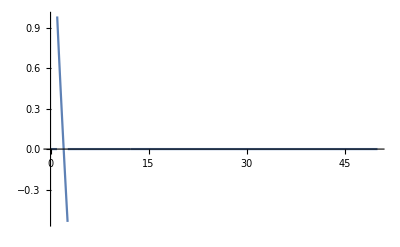

```mathematica
Plot[%89,{x,0,50},PlotRange->All]
```

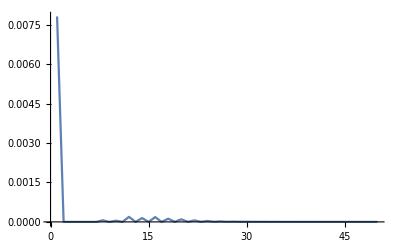

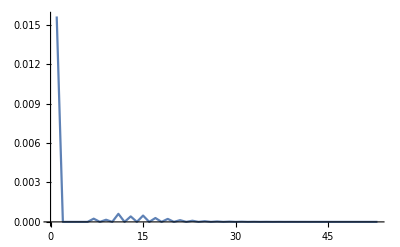

```mathematica
ListLinePlot[dec[[2;;n-2]]/.s[[1]],PlotRange->All]
```